#### Neuronal decoding of temperature signals in Caenorhabditis elegans Contribution by- Abhilasha Batra cGMP signal transduction pathway (Fig. 1b) -Graphics-

#### Signal (S) used in the model

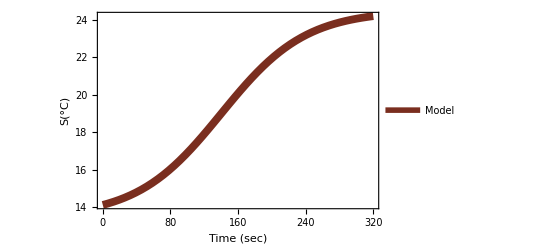

```mathematica
S = Plot[(a/(1+(Exp[-β(t-tm)]))+b)/.{a-> 11,b-> 13.5,β-> 0.02, tm-> 140},{t,0,320},BaseStyle->{32,FontFamily->"Helvetica"},Frame-> True,FrameLabel-> {Style["Time (sec)",38], Style["S(°C)",38]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}, PlotStyle->{Thickness[0.014],CMYKColor[0.2,0.7,0.8,0.4]},PlotLegends->LineLegend[{"Model"},LabelStyle->Directive[30]]]
```

#### Comparison of signal in the model to signal provided in experiments by Kobayashi et al.

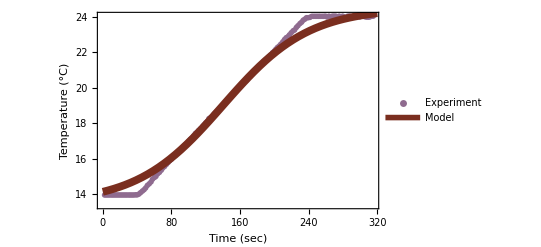

```mathematica
data1=Import["Fig1d_Kobayashi.csv"];
f1 = Show[ListPlot[data1,BaseStyle->{32,FontFamily->"Helvetica"},PlotMarkers->{ "OpenMarkers",Offset[8]},PlotStyle->{CMYKColor[0.2,0.4,0.2,0.3]},Frame-> True,FrameLabel->{Style["Time (sec)",38], Style["Temperature (°C)",38]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400},PlotLegends->PointLegend[{"Experiment"},LabelStyle->Directive[30]]],Plot[(11/(1+(Exp[-0.02(t-140)]))+13.5),{t,0,320},BaseStyle->{32,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.014],CMYKColor[0.2,0.7,0.8,0.4]},PlotLegends->LineLegend[{"Model"},LabelStyle->Directive[30]]]]
```

#### Signal processing in the AFD neurons: S* encoding at the sensory endings

Absolute signal encoding: S* =  S

{{cg[t]→InterpolatingFunction[…][t],ca[t]→InterpolatingFunction[…][t]}}

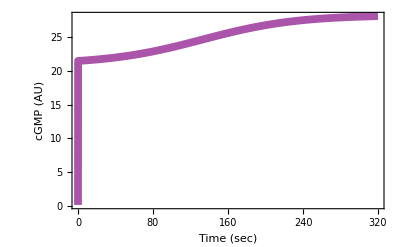

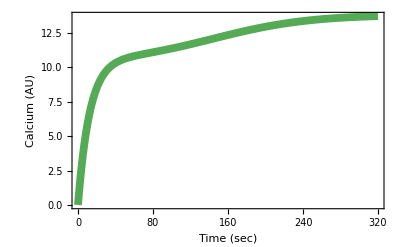

```mathematica
S = (a/(1+(Exp[-β(t-tm)]))+b)/.{a-> 11,b-> 13.5,β-> 0.02, tm-> 140};
p1 =Plot[S, {t,0,320},BaseStyle->{32,FontFamily->"Helvetica"},Frame-> True,FrameLabel-> {Style["Time (sec)",38], Style["S(°C)",38]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}, PlotStyle->{Thickness[0.014],CMYKColor[0.2,0.7,0.8,0.4]},(*PlotLegends->LineLegend[{"Model"},*)LabelStyle->Directive[30]];
model1= NDSolve[{(((kr*(1/(λ*Tc))*R*(S)))-((kpde*(cg[t])^2)/((Kmpde)+(cg[t]))))== cg'[t],(ef*ic*((cg[t])^n/((Kcg)^n+(cg[t])^n))-(kc*(ca[t]-0.1)))== ca'[t],cg[0]== 0,ca[0]== 0.1}/.{Tc-> 20, kr->3.2648*10^-6,λ-> 1,R->10^6, kpde->1*10^6,Kmpde-> 2,ef-> 32.33*10^12, ic->8*10^-12 ,Kcg-> 8.4,n->  0.97,kc->0.08},{cg[t],ca[t]},{t,0,320},AccuracyGoal->8,PrecisionGoal->8]
pm11 =Plot[{cg[t]/10^-4}/.model1,{t,0,320},BaseStyle->{32,FontFamily->"Helvetica"},PlotRange-> All,PlotStyle->{Thickness[0.014],Blend[{Red,Blue,White}]},Frame-> True, FrameLabel-> {Style["Time (sec)",38], Style["cGMP (AU)",38]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}(*,PlotLegends->LineLegend[{"cGMP response"}]*)]
pm21 =Plot[{(ca[t]-0.1)/0.1}/.model1,{t,0,320},BaseStyle->{32,FontFamily->"Helvetica"},PlotRange-> All,PlotStyle->{ Thickness[0.014],Blend[{Green, Black,White}]},Frame-> True, FrameLabel-> {Style["Time (sec)",38],Style[ "Calcium (AU)",38]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}(*,PlotLegends->LineLegend[{"Calcium response"}]*)]
```

First derivative signal encoding: S* = dS/dt

{{cg[t]→InterpolatingFunction[…][t],ca[t]→InterpolatingFunction[…][t]}}

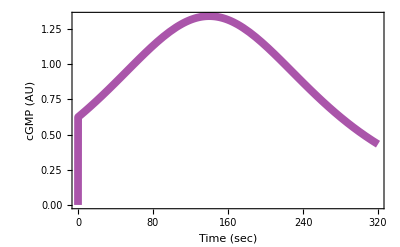

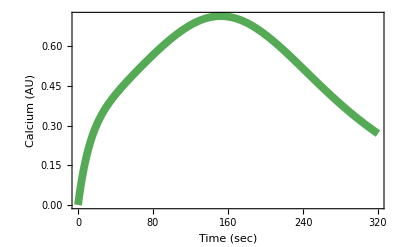

```mathematica
dS = D[S, t];
p2 =Plot[(dS), {t,0,320},BaseStyle->{32,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.014],CMYKColor[0.9,0.7,0.2,0.4]},Frame-> True,FrameLabel-> {Style["Time (sec)",38],Style[ "dS/dt (°C/sec)",38]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}(*,PlotLegends->LineLegend[{"Derivative of Signal"}]*)];
model2= NDSolve[{(((kr*(1/(λ*Tc))*R*(dS)))-((kpde*(cg[t])^2)/((Kmpde)+(cg[t]))))== cg'[t],(ef*ic*((cg[t])^n/((Kcg)^n+(cg[t])^n))-(kc*(ca[t]-0.1)))== ca'[t],cg[0]== 0,ca[0]== 0.1}/.{Tc-> 20, kr->3.2648*10^-6,λ-> 1,R->10^6, kpde->1*10^6,Kmpde-> 2,ef-> 32.33*10^12, ic->8*10^-12 ,Kcg-> 8.4,n->  0.97,kc->0.08},{cg[t],ca[t]},{t,0,320},AccuracyGoal->8,PrecisionGoal->8]
pm11 =Plot[{cg[t]/10^-4}/.model2,{t,0,320},BaseStyle->{32,FontFamily->"Helvetica"},PlotRange-> All,PlotStyle->{Thickness[0.014],Blend[{Red,Blue,White}]},Frame-> True, FrameLabel-> {Style["Time (sec)",38], Style["cGMP (AU)",38]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}(*,PlotLegends->LineLegend[{"cGMP response"}]*)]
pm21 =Plot[{(ca[t]-0.1)/0.1}/.model2,{t,0,320},BaseStyle->{32,FontFamily->"Helvetica"},PlotRange-> All,PlotStyle->{ Thickness[0.014],Blend[{Green, Black,White}]},Frame-> True, FrameLabel-> {Style["Time (sec)",38],Style[ "Calcium (AU)",38]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}(*,PlotLegends->LineLegend[{"Calcium response"}]*)]
```

Relation between response time and growth temperature

```mathematica
responsetime(*(Subscript[t, R])*)= Solve[((a/(1+(Exp[-β(tr-tm)]))+b)== (0.79Tc+3.1))/.{a-> 8,b-> 13.5,β-> 0.02, tm-> 140,Tc-> 21},{tr}](*Tr = (0.79Tc+3.1) From SI Table [1]*)
responsetemp(*(T^*)*)=Simplify[(a/(1+(Exp[-β(tr-tm)]))+b)/.{a-> 8,b-> 13.5,β-> 0.02, tm-> 140,Tc-> 21}]/.{responsetime}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{tr→201.48}}

{{19.69}}

#### Effect of growth-temperature memory on response dynamics of AFD neurons

For T_C=17^oC

{{cg[t]→InterpolatingFunction[…][t],ca[t]→InterpolatingFunction[…][t]}}

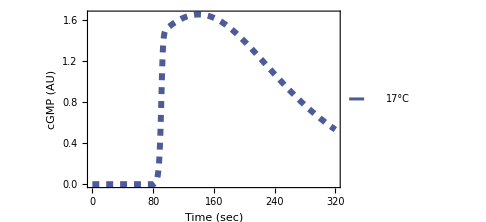

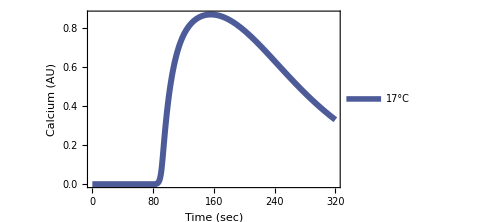

```mathematica
S = (a/(1+(Exp[-β(t-tm)]))+b)/.{a-> 11,b-> 13.5,β-> 0.02, tm-> 140};
dS = D[S,t];
model17= NDSolve[{(((kr*(1/(λ*Tc))*R*(dS)*(1/(1+ⅇ^(1/τ(91.64-t))))))-((kpde*(cg[t])^2)/((Kmpde)+(cg[t]))))== cg'[t],(ef*ic*((cg[t])^n/((Kcg)^n+(cg[t])^n))-(kc*(ca[t]-0.1)))== ca'[t],cg[0]== 0,ca[0]== 0.1}/.{Tc-> 17, kr->3.2648*10^-6,λ-> 1,R->1.3*10^6,τ-> 1, kpde->1*10^6,Kmpde-> 2,ef-> 32.33*10^12, ic->8*10^-12 ,Kcg-> 8.4,n->  0.97,kc->0.08},{cg[t],ca[t]},{t,0,320},AccuracyGoal->8,PrecisionGoal->8]
pm117 =Plot[{cg[t]/10^-4}/.model17,{t,0,320},BaseStyle->{18,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.012],Dashed,CMYKColor[0.5,0.4,0,0.4]},Frame-> True, FrameLabel-> {"Time (sec)", "cGMP (AU)"},FrameStyle->Directive[Black,Thickness[0.006]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->Medium,PlotLegends->LineLegend[{"17°C"}]]
pm217 =Plot[{(ca[t]-0.1)/0.1}/.model17,{t,0,320},BaseStyle->{18,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.012],CMYKColor[0.5,0.4,0,0.4]},Frame-> True, FrameLabel-> {"Time (sec)", "Calcium (AU)"},FrameStyle->Directive[Black,Thickness[0.006]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->Medium,PlotLegends->LineLegend[{"17°C"}]]
```

For T_C=20^oC

{{cg[t]→InterpolatingFunction[…][t],ca[t]→InterpolatingFunction[…][t]}}

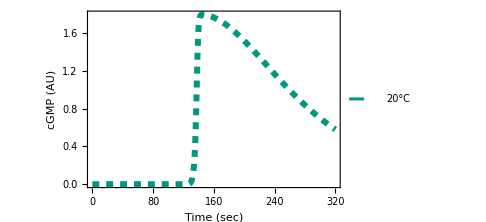

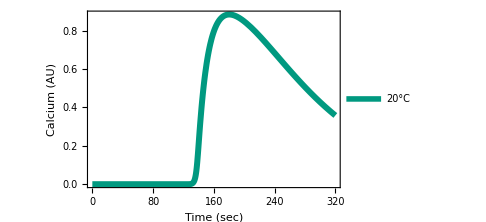

```mathematica
S = (a/(1+(Exp[-β(t-tm)]))+b)/.{a-> 11,b-> 13.5,β-> 0.02, tm-> 140};
dS = D[S,t];
model20= NDSolve[{(((kr*(1/(λ*Tc))*R*(dS)*(1/(1+ⅇ^(1/τ(138.18-t))))))-((kpde*(cg[t])^2)/((Kmpde)+(cg[t]))))== cg'[t],(ef*ic*((cg[t])^n/((Kcg)^n+(cg[t])^n))-(kc*(ca[t]-0.1)))== ca'[t],cg[0]== 0,ca[0]== 0.1}/.{Tc-> 20, kr->32648*10^-10,λ-> 1,R->1.8*10^6,τ-> 1, kpde->1*10^6,Kmpde-> 2,ef-> 32.33*10^12, ic->8*10^-12 ,Kcg-> 8.4,n->  0.97,kc->0.08},{cg[t],ca[t]},{t,0,320},AccuracyGoal->8,PrecisionGoal->8]
pm120 =Plot[{cg[t]/10^-4}/.model20,{t,0,320},BaseStyle->{18,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.012],Dashed,CMYKColor[1,0.4,0.5,0]},Frame-> True, FrameLabel-> {"Time (sec)", "cGMP (AU)"},FrameStyle->Directive[Black,Thickness[0.006]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->Medium,PlotLegends->LineLegend[{"20°C"}]]
pm220 =Plot[{(ca[t]-0.1)/0.1}/.model20,{t,0,320},BaseStyle->{18,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.012],CMYKColor[1,0.4,0.5,0]},Frame-> True, FrameLabel-> {"Time (sec)", "Calcium (AU)"},FrameStyle->Directive[Black,Thickness[0.006]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->Medium,PlotLegends->LineLegend[{"20°C"}]]
```

For T_C=23^oC

{{cg[t]→InterpolatingFunction[…][t],ca[t]→InterpolatingFunction[…][t]}}

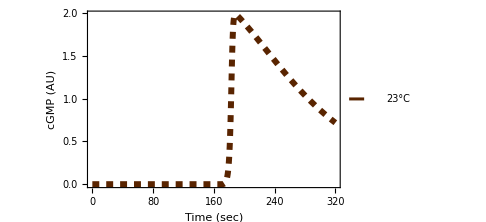

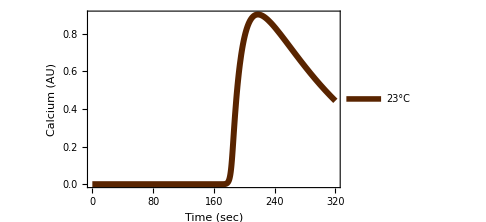

```mathematica
S = (a/(1+(Exp[-β(t-tm)]))+b)/.{a-> 11,b-> 13.5,β-> 0.02, tm-> 140};
dS = D[S,t];
model23= NDSolve[{(((kr*(1/(λ*Tc))*R*(dS)*(1/(1+ⅇ^(1/τ(183.88-t))))))-((kpde*(cg[t])^2)/((Kmpde)+(cg[t]))))== cg'[t],(ef*ic*((cg[t])^n/((Kcg)^n+(cg[t])^n))-(kc*(ca[t]-0.1)))== ca'[t],cg[0]== 0,ca[0]== 0.1}/.{Tc-> 23, kr->32648*10^-10,λ-> 1,R->3.2*10^6, τ-> 1,kpde->1*10^6,Kmpde-> 2,ef-> 32.33*10^12, ic->8*10^-12 ,Kcg-> 8.4,n->  0.97,kc->0.08},{cg[t],ca[t]},{t,0,320},AccuracyGoal->8,PrecisionGoal->8]
pm123 =Plot[{cg[t]/10^-4}/.model23,{t,0,320},BaseStyle->{18,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.012],Dashed,CMYKColor[0.5,0.8,1,0.3]},Frame-> True, FrameLabel-> {"Time (sec)", "cGMP (AU)"},FrameStyle->Directive[Black,Thickness[0.006]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->Medium,PlotLegends->LineLegend[{"23°C"}]]
pm223 =Plot[{(ca[t]-0.1)/0.1}/.model23,{t,0,320},BaseStyle->{18,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.012],CMYKColor[0.5,0.8,1,0.3]},Frame-> True, FrameLabel-> {"Time (sec)", "Calcium (AU)"},FrameStyle->Directive[Black,Thickness[0.006]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->Medium,PlotLegends->LineLegend[{"23°C"}]]
```

For T_C shift from 17 to 23^oC

{{cg[t]→InterpolatingFunction[…][t],ca[t]→InterpolatingFunction[…][t]}}

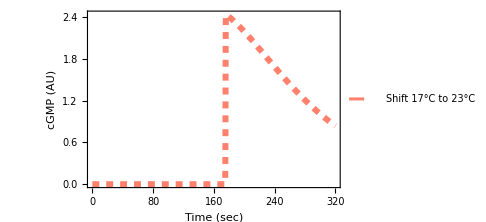

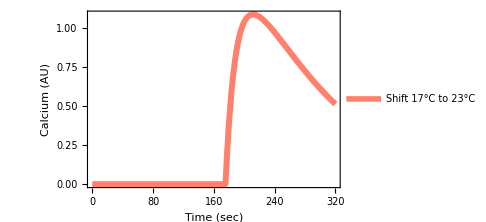

```mathematica
S = (a/(1+(Exp[-β(t-tm)]))+b)/.{a-> 11,b-> 13.5,β-> 0.02, tm-> 140};
dS = D[S,t];models1723= NDSolve[{(((kr*(1/(λ*Tc))*R*(dS)*(1/(1+ⅇ^(1/τ(91.64-t)+a1/τ(183.88-t))))))-((kpde*(cg[t])^2)/((Kmpde)+(cg[t]))))== cg'[t],(ef*ic*((cg[t])^n/((Kcg)^n+(cg[t])^n))-(kc*(ca[t]-0.1)))== ca'[t],cg[0]== 0,ca[0]== 0.1}/.{Tc->17, kr->32648*10^-10,λ-> 1,R->3.2*10^6, a1->10,τ-> 1,kpde->1*10^6,Kmpde-> 2,ef-> 32.33*10^12, ic->8*10^-12 ,Kcg-> 8.4,n->  0.97,kc->0.08},{cg[t],ca[t]},{t,0,320}]
pm123s =Plot[{cg[t]/10^-4}/.models1723,{t,0,320},BaseStyle->{18,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.012],Dashed,Blend[{Red,LightYellow}]},Frame-> True, FrameLabel-> {"Time (sec)", "cGMP (AU)"},FrameStyle->Directive[Black,Thickness[0.006]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->Medium,PlotLegends->LineLegend[{"Shift 17°C to 23°C"}]]
pm223s =Plot[{(ca[t]-0.1)/0.1}/.models1723,{t,0,320},BaseStyle->{18,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.012],Blend[{Red,LightYellow}]},Frame-> True, FrameLabel-> {"Time (sec)", "Calcium (AU)"},FrameStyle->Directive[Black,Thickness[0.006]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->Medium,PlotLegends->LineLegend[{"Shift 17°C to 23°C"}]]
```

#### Response dynamics for different thermal stimuli

Effect of change in the slope of thermal ramp

Change value of β to control the rate of change of signal

```mathematica
responsetime(*(Subscript[t, R])*)= Solve[((a/(1+(Exp[-β(tr-tm)]))+b)== (0.79Tc+3.1))/.{a-> 14,b-> 12,β-> 0.01, tm-> 140,Tc-> 20},{tr}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{tr→137.143}}

{{cg[t]→InterpolatingFunction[…][t],ca[t]→InterpolatingFunction[…][t]}}

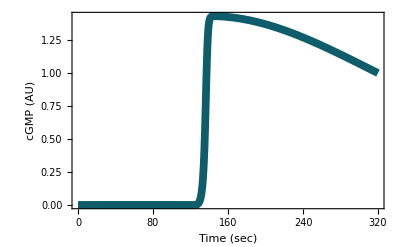

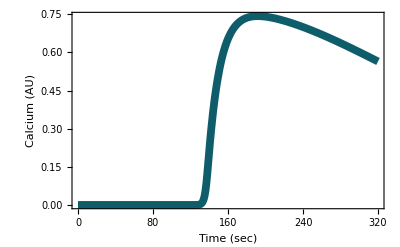

```mathematica
S1s = (a/(1+(Exp[-β(t-tm)]))+b)/.{a-> 14,b-> 12,β-> 0.01, tm-> 140};
p11s = Plot[S1s, {t,0,320}];
dS1s= D[S1s, t];
p12s =Plot[(dS1s), {t,0,320}];
model201s= NDSolve[{(((kr*(1/(λ*Tc))*R*(dS1s)(1/(1+ⅇ^(1/τ(137.142-t))))))-((kpde*(cg[t])^2)/((Kmpde)+(cg[t]))))== cg'[t],(ef*ic*((cg[t])^n/((Kcg)^n+(cg[t])^n))-(kc*(ca[t]-(0.1))))== ca'[t],cg[0]== 0,ca[0]== 0.1}/.{Tc-> 20, kr->32648*10^-10,λ-> 1,R->1.8*10^6,τ-> 1,kpde->1*10^6,Kmpde-> 2,ef-> 32.33*10^12, ic->8*10^-12 ,Kcg-> 8.4,n->  0.97,kc->0.08},{cg[t],ca[t]},{t,0,320},AccuracyGoal->8,PrecisionGoal->8]
pm1201s=Plot[{cg[t]/10^-4}/.model201s,{t,0,320},BaseStyle->{26,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.014],CMYKColor[0.9,0.4,0.3,0.4]},Frame-> True, FrameLabel-> {Style["Time (sec)",32], Style["cGMP (AU)",32]},FrameStyle->Directive[CMYKColor[0.9,0.4,0.3,0.4],Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400},PlotRange->All]
pm2201s =Plot[{(ca[t]-0.1)/0.1}/.model201s,{t,0,320},BaseStyle->{26,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.014],CMYKColor[0.9,0.4,0.3,0.4]},Frame-> True, FrameLabel-> {Style["Time (sec)",32], Style["Calcium (AU)",32]},FrameStyle->Directive[CMYKColor[0.9,0.4,0.3,0.4],Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400},PlotRange->All]
```

Effect of change in the step size of thermal ramp

Change value of ‘a’ and ‘b’ to change the range of signal

```mathematica
responsetime(*(Subscript[t, R])*)= Solve[((a/(1+(Exp[-β(tr-tm)]))+b)== (0.79Tc+3.1))/.{a-> 5,b-> 17,β-> 0.02, tm-> 140,Tc-> 20},{tr}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{tr→115.523}}

{{cg[t]→InterpolatingFunction[…][t],ca[t]→InterpolatingFunction[…][t]}}

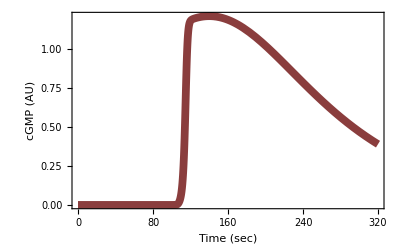

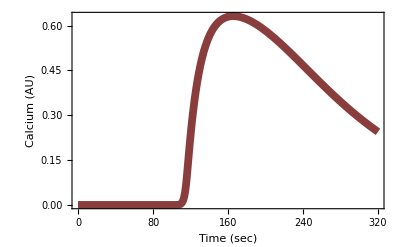

```mathematica
S1r = (a/(1+(Exp[-β(t-tm)]))+b)/.{a-> 5,b-> 17,β-> 0.02, tm-> 140};
p11r = Plot[S1r, {t,0,320}];
dS1r = D[S1r,t];
p21r =Plot[(dS1r), {t,0,320}];
model201r= NDSolve[{(((kr*(1/(λ*Tc))*R*(dS1r)(1/(1+ⅇ^(1/τ(115.52258-t))))))-((kpde*(cg[t])^2)/((Kmpde)+(cg[t]))))== cg'[t],(ef*ic*((cg[t])^n/((Kcg)^n+(cg[t])^n))-(kc*(ca[t]-(0.1))))== ca'[t],cg[0]== 0,ca[0]== 0.1}/.{Tc-> 20, kr->32648*10^-10,λ-> 1,R->1.8*10^6,τ-> 1,kpde->1*10^6,Kmpde-> 2,ef-> 32.33*10^12, ic->8*10^-12 ,Kcg-> 8.4,n->  0.97,kc->0.08},{cg[t],ca[t]},{t,0,320}]
pm1201r=Plot[{cg[t]/10^-4}/.model201r,{t,0,320},BaseStyle->{26,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.014],CMYKColor[0.1,0.6,0.6,0.4]},Frame-> True, FrameLabel-> {Style["Time (sec)",32], Style["cGMP (AU)",32]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}]
pm2201r=Plot[{(ca[t]-0.1)/0.1}/.model201r,{t,0,320},BaseStyle->{26,FontFamily->"Helvetica"},PlotStyle->{Thickness[0.014],CMYKColor[0.1,0.6,0.6,0.4]},Frame-> True, FrameLabel-> {Style["Time (sec)",32], Style["Calcium (AU)",32]},FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,Thickness[0.004]],ImageSize->{Automatic,400}]
```